```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
```

#### Trigger size as function of density (see Woosley, check with SR).

```mathematica
trigger[ρ_]:=Piecewise[{{10^-5*(ρ/(5*10^9))^(-1/2),ρ>10^8},{1/(10000 √2)*(ρ/10^8)^-2,ρ<=10^8}}]
```

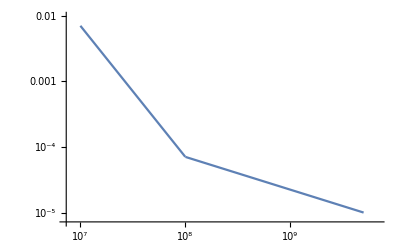

```mathematica
LogLogPlot[{trigger[ρ]},{ρ,5*10^9,10^7}]
```

#### Import data thief of WD mass-density + WD mass-radius relations (stored on VN local drive)

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
```

```mathematica
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
```

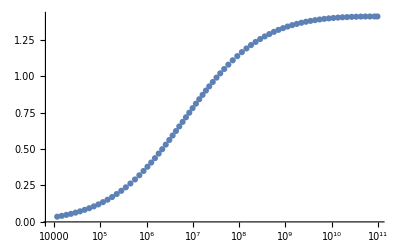

```mathematica
ListLogLinearPlot[WD]
```

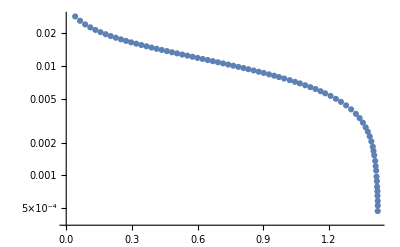

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Massreverse=Interpolation[Reverse/@WD];
```

```mathematica
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### λ_T as function of mass

```mathematica
triggermass=Interpolation[Table[{WDplot[ρ],trigger[ρ]},{ρ,fSpace[10^6,5*10^9,1000]}]];
```

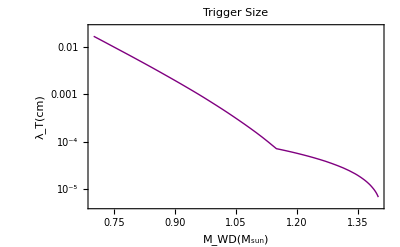

```mathematica
LogPlot[triggermass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### V_esc

```mathematica
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

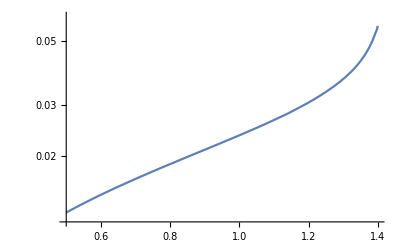

```mathematica
LogPlot[vesc[M],{M,0.5,1.4}]
```

#### τ_d (for trigger size) scales as 1/ρ by definition. Diffusion time vs. transit time comparision - need to check τ_d!

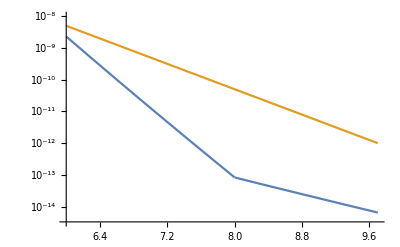

```mathematica
LogPlot[{Convert[(trigger[10^ρ]Centimeter)/(vesc[WDplot[10^ρ]]SpeedOfLight),Second] 1/Second,10^-12((5*10^9)/10^ρ)},{ρ,Log10[10^6],Log10[5*10^9]}]
```

#### Transit upper bound (flux is too low) for a single WD

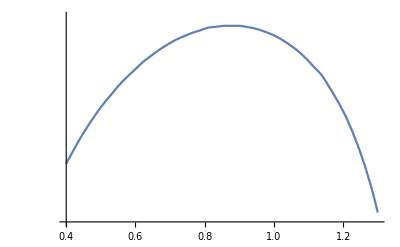

```mathematica
LogPlot[Convert[Subscript[ρ, DM] (Giga*ElectronVolt)/Centimeter^3*Giga Year*Pi*(Radplot[M]SolarRadius)^2*(vesc[M])^2/(10^-3)1/SpeedOfLight*SpeedOfLight^2,Giga ElectronVolt] 1/(Giga ElectronVolt)/.{Subscript[ρ, DM]->10^3},{M,0.4,1.3}]
```

#### Q-ball Boom:

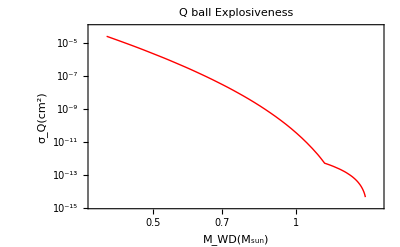

```mathematica
LogLogPlot[1/10^4*(Interpolation[triggermass][M])^2,{M,0.4,1.4},FrameLabel->{"M_WD(M_sun)","σ_Q(cm^2)"},PlotLabel->"Q ball Explosiveness",Frame->True,PlotStyle->{Thick,Red},FrameStyle->Black]
```

#### Minimum E_boom for different densities

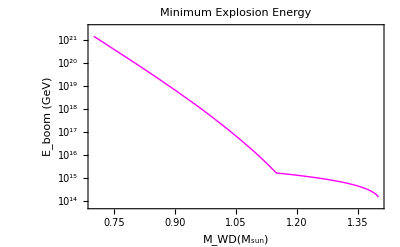

```mathematica
LogPlot[Convert[(Massreverse[M]*Gram/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*(triggermass[M]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d],{M,0.7,1.4},FrameLabel->{"M_WD(M_sun)","E_boom (GeV)"},PlotLabel->"Minimum Explosion Energy",Frame->True,PlotStyle->{Thick,Magenta},FrameStyle->Black]
```

#### Crust stopping calculation (R_c~ km, ρ_c~ ρ_interior)

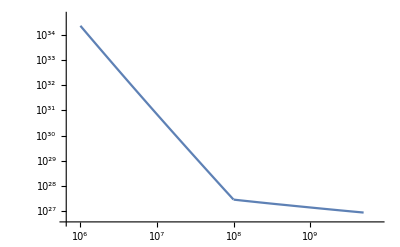

```mathematica
LogLogPlot[Convert[((Mega ElectronVolt)/vesc[WDplot[ρ]]^2*(trigger[ρ]*Centimeter)^2*ρ Gram/Centimeter^3*1/(12 Giga ElectronVolt)*SpeedOfLight^2(1Kilo Meter))1/(Giga ElectronVolt),d],{ρ,10^6,5*10^9}]
```